# Skeleton Analysis of Melt Network

## Functions

```mathematica
(*Clear["Global`*"];*)
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	(*If[Length[AdjacencyList[graph,i]]>2,AppendTo[ans,{i,Length[AdjacencyList[graph,i]]}]]];*)
	degree = VertexDegree[graph,i];
	If[degree>2,AppendTo[ans,{i,degree}]]];
	ans
]
```

mergeScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {identifier, degree, {x1,y1,z1}, r1} 
	ball2: {identifier, degree, {x2,y2,z2}, r2}

```mathematica
mergeScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦4⟧,ball2⟦4⟧];
	r2 = Min[ball1⟦4⟧,ball2⟦4⟧];
	d = EuclideanDistance[ball1⟦3⟧, ball2⟦3⟧];
	score = (r1 + r2 - d)/(2*r2);
	score
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Return[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = deleteNode[g, nodesDeg2⟦1⟧];
		nodesDeg2 = Drop[nodesDeg2,1];
	];
	g
]
```

smallestCircumBall[ball1,ball2] computes the smallest circumscribe ball of ball1 and ball2
Inputs:
	ball: {identifier, degree, {x,y,z},r}
Return:
	{c,r}: c is the center and r is the radius

```mathematica
smallestCircumBall:=Function[{ball1,ball2},
	c1 = ball1⟦3⟧;
	r1 = ball1⟦4⟧;
	c2 = ball2⟦3⟧;
	r2 = ball2⟦4⟧;
	d = EuclideanDistance[c1, c2];
	
	If[d == 0, Throw[{c1,Max[r1,r2]}]];
	
	t1 = r1/d;
	t2 = -r1/d;
	t3 = 1+r2/d;
	t4 = 1-r2/d;
	tmax = Max[t1,t2,t3,t4];
	tmin = Min[t1,t2,t3,t4];
	c3 = c1 + (tmax+tmin)/2*(c2-c1);
	r3 = (Abs[tmax]+Abs[tmin])/2*d;
	{c3,r3}
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
inputs:
	junctionList: list of all junctions: {identifier, degree, {x,y,z},r}
	graph: the simplified graph showing connectivity relationship of junctions
	ball: {identifier, degree, {x,y,z},r}
return: 
	a list consisting of an updated junction list and an updated graph

```mathematica
mergeJunctions:= Function[{junctionList, graph, ball1, ball2},
	newJunctionList = junctionList;

	v1 = ball1⟦1⟧;
	v2 = ball2⟦1⟧;
	innerEdges = EdgeList[graph,v1<->v2];
	
	g = EdgeDelete[graph, innerEdges];
	g = VertexReplace[g,{v2->v1}];
	
	newDegree = VertexDegree[g,v1];
	
	{c3,r3}= Catch[smallestCircumBall[ball1,ball2]];
	
	newBall = {v1,newDegree,c3,r3};
	
	newJunctionList = DeleteCases[newJunctionList,ball1];
	newJunctionList = DeleteCases[newJunctionList,ball2];
	newJunctionList = AppendTo[newJunctionList,newBall];
	
	{newJunctionList, g}
]
```

```mathematica
x = {{1,3,5},{1,7,6},{2,4,5}};
y = DeleteCases[x,{2,4,5}]
```

{{1,3,5},{1,7,6}}

```mathematica
computeCN:=Function[{junctionList,graph},
	J = junctionList;
	G = graph;
	threshold = 0;
	While[True,
		maxScore = threshold-1;
		tgt1 = {};
		tgt2 = {};
		
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			ball1 = Select[J,#⟦1⟧ == j1 &];
			ball2 = Select[J,#⟦1⟧ == j2 &];
			
			If[ball1 == {} || ball2 == {}, Continue[]];
			
			ball1 = ball1⟦1⟧;
			ball2 = ball2⟦1⟧;
			
			score = mergeScore[ball1,ball2];
			If[score > maxScore,
				maxScore = score;
				tgt1 = ball1;
				tgt2 = ball2;
			]
		,{edge,edges}];
		
		If[maxScore < threshold,Break[]];
		{J,G} = mergeJunctions[J,G,tgt1,tgt2];
		Print[{maxScore,Length[J]}];
	];
	{J,G}
]
```

## Function Test

### test data

```mathematica
testG =
```

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};
(*testLines = {{1,2},{1,2}};*)
g = linesToGraph[testLines]
```

-Graphics-

test deleteNode[graph, v], simplifyGraph[graph]

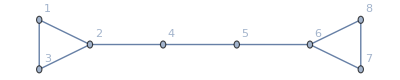

-Graphics3D-

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
s = simplifyGraph[g];
GraphPlot3D[s]
```

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

1/4 (8-3 √3)

test simplifyGraph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
h = simplifyGraph[g];
GraphPlot3D[h]
```

-Graphics-

-Graphics3D-

test smallestCircumBall

```mathematica
c1 = {0,0,0};
r1 = 1;
c2 = {0.1,0.5,0.6};
r2 = 0.4;
{c3,r3} = smallestCircumBall[{1,2,c1,r1},{1,2,c2,r2}]

a1 = Ball[c1,r1];
a2 = Ball[c2,r2];
a3 = Ball[c3,r3];

Graphics3D[{
	Opacity[0.5],
	Green,a1,
	Blue,a2,
	Red,a3}]
```

{{0.0119,0.0594998,0.0713998},1.0937}

-Graphics3D-

## Code

### Set working directory

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

### Import data from files

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

```mathematica
maRawData = Import["data\\scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;

maPoints = maTable⟦;;86117,;;⟧;
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

```mathematica
numOfPoints = 12326;
numOfEdges = 12468;

skelRawData = Import["data\\scoba12_small_skel_0.1.ply","Table"];
skelTable = skelRawData⟦15;;,;;⟧;

skelPoints = skelTable⟦;;numOfPoints,3;;5⟧;
skelLines = skelTable⟦numOfPoints+1;;⟧ + 1;
skelRadius = skelTable⟦;;numOfPoints,2⟧;
```

align coordinates

```mathematica
maPoints = coordsAlign[maPoints,skelPoints];
```

### Processing data of scoba12 and skeletons

#### Ground Truth

trueJunctions: N by 5 (x, y, z, CN, diameter)

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

#### Median Axes

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

#### Skeleton data

```mathematica
skelGraph = linesToGraph[skelLines];
junctions = getJunctions[skelGraph];
junctionBalls = Table[{Ball[skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧]},{i,Dimensions[junctions]⟦1⟧}];
junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}];
```

## Real-World Data Test & Visualization

validate visualization of median axes

```mathematica
maGraphic = Import["data\\scoba12_small.ply","Graphics3D"];
(*Show[Graphics3D[polygonInCoords],maGraphic]*)
```

validate visualization of skeleton

```mathematica
edgeInCoords = Table[{Opacity[0.5],Green,Thickness[0.004],Line[{skelPoints⟦skelLine⟦1⟧⟧,skelPoints⟦skelLine⟦2⟧⟧}]},{skelLine,skelLines}];
```

```mathematica
skelGraphic = Import["data\\scoba12_small_skel_0.1.ply","Graphics3D"];

Show[Graphics3D[edgeInCoords],skelGraphic]
```

-Graphics3D-

show junction balls in median axes

```mathematica
Show[Graphics3D[{edgeInCoords,{Opacity[1],Blue,junctionBalls}}], maGraphic]
Show[Graphics3D[{edgeInCoords,{Opacity[0.5],Blue,junctionBalls}}]]
```

-Graphics3D-

-Graphics3D-

```mathematica
simplifiedG = simplifyGraph[skelGraph];
GraphPlot3D[simplifiedG]
```

-Graphics3D-

```mathematica
{J2,G2}=computeCN[junctionsDataTable,simplifiedG];
```

```mathematica
J2
```

{{2,3,{-4.5,2.5,1.5},1.66304},{117,3,{38.5,-53.5,7.5},0.866025},{223,3,{-6.5,41.5,-65.5},2.98333},{358,3,{-36.5,-13.5,-11.5},1.55249},{376,3,{-53.5,14.5,-43.5},1.78295},{595,3,{-47,-12,61},1.3171},{818,3,{54,-22.5,42},1.07311},{854,3,{52.5,28.5,60.5},1.17139},{1056,3,{32.5,56.5,19.5},0.933012},{1103,3,{32.5,35.5,29},0.992027},{1415,3,{-8.3,-54.1,-8.9},0.866025},{1490,3,{35.5,-43.5,-34.5},2.08346},{1564,3,{43.5,-45.5,-46.5},1.02813},{1574,3,{42.5,-47.5,-43.5},0.992027},{1601,4,{42.5,-37.5,-61.5},1.65831},{1602,3,{47.714,-39.3571,-57.5},1.69968},{1668,3,{-50.5,-36.9286,-37.0714},1.26217},{1717,3,{-42.5,-56.5,2.5},1.74402},{1726,3,{-32.5,-57.5,-7.5},2.56465},{1729,3,{-33.5,-50.5,-9.5},2.20302},{1817,3,{-28.5,-52.5,-11.8333},1.98835},{1841,3,{-13.5,-50.5,-10},0.933012},{1924,3,{-10.25,-13.5,-5.6667},0.59512},{2005,3,{-48.7,-9.22,-18.78},1.02813},{2023,3,{-50.75,-8,-11.5},1.85754},{2041,3,{-52.4,-17.2,-24.6},1.10487},{2087,3,{-50,-22,-27},2.02346},{2106,3,{-50.5,-8.5,-23},3.01816},{2121,3,{-52,-2.5,-28},1.19911},{2134,3,{-51.2143,-3.5,-25.7857},1.15413},{2168,3,{-44.5,24,-58.5},1.21745},{2209,3,{-45,15.5,-49},1.28019},{2250,3,{-50,22,-46.5},0.866025},{2251,3,{-49.3,22.4,-48.4},0.866025},{2291,3,{-53.5,6.5,-37.8333},1.11803},{2364,3,{-37.9,27.1,-60.4},2.10838},{2569,3,{-6.0455,43.136,-39.8636},0.992027},{2588,3,{-21.1154,51.5,-66.4231},1.30383},{2985,3,{-14.9925,19.0075,-26.8582},0.866025},{2989,3,{-16.2333,25.5667,-18.5},0.992027},{3055,3,{-31,16.5,-26.5},1.72239},{3111,3,{-49.54,-1.5,-23.9},1.11803},{3132,3,{-48,5.25,-33},1.20096},{3454,3,{-15.1667,4.8333,19.5},2.2394},{3643,3,{-38.1667,36.5,46.167},2.18913},{3707,3,{-12.3333,48,36.333},1.26217},{3828,3,{-12.5,31.5,50.5},1.89572},{3884,3,{-36,-6.5,59},2.09982},{3903,3,{-26.9,24.9,42.5},0.729298},{3969,3,{-36.5,-3.5,56.5},0.933012},{4099,3,{-48.5,-25,70},0.992027},{4205,3,{-51.5,-56,7.5},1.19911},{4232,3,{-39.5667,-45.3,13.1667},0.992027},{4291,3,{-49.3333,-9.3333,14.3333},1.47891},{4308,3,{-46.0714,-0.9286,22.6429},1.53053},{4455,3,{-25.5,-16.8333,0.5},1.14012},{4487,3,{-8.3571,0.214298,15.6429},1.38817},{4495,3,{-7.4231,-0.115398,13.0385},1.11803},{4619,3,{37.5,-45.5,21.5},1.24975},{4661,4,{37.9118,-31.4412,42.618},1.68385},{4884,3,{11.5,11.5,37.5},1.20749},{4935,3,{27.8333,25.8333,38.1},1.26217},{4952,3,{25.5,30.5,38.5},1.23521},{4962,3,{29.5,33.5,32.5},1.02813},{5525,3,{36,44.5,-8},1.26217},{5702,3,{3.2692,-2.4231,-18.8846},1.73055},{5710,3,{1.5,-36.5,-5.3},0.992027},{5786,3,{18.5,-56.3,-7.3},0.933012},{5796,3,{23.5,-48.5,-14.5},1.02813},{5919,3,{34.5,-57.5,-7.5},2.08573},{6018,3,{40.5,-38.5,-54.5},3.50419},{6079,3,{51.1667,-23.3333,41.3333},0.866025},{6135,3,{47.1357,32.2952,-10.431},0.866025},{6448,3,{-7.21153,42.654,-41.9423},0.866025},{6452,3,{43.8333,-46.5833,-44.8333},0.866025},{6883,3,{-31.8333,29.3333,-62.3333},1.28019},{6952,3,{-13.3359,18.6179,-26.1154},0.866025},{7041,3,{-55.3333,6.83333,15.6667},0.866025},{7114,3,{-11.6111,3.16667,17.4444},0.866025},{7129,3,{21.1667,52.8333,22.5},1.41421},{7173,3,{-6.91665,29.6666,46.75},1},{7263,3,{25,-4.33333,39.3333},1.5459},{7284,3,{-44.1048,-28.2857,68.9033},0.866025},{7304,3,{-48.8333,-56.5,8.72223},1.22474},{7386,3,{-10.5833,-15,1.83333},1.29904},{7482,3,{37.1667,-52.1667,23.5},0.866025},{7591,3,{43.8333,-27.9444,42.389},1},{7801,3,{37.8333,17.1667,36.5},2.03101},{7860,3,{4.83333,19.1667,43.1667},0.866025},{7926,3,{6.7963,15.9444,41.926},1.34983},{8536,3,{26.8333,-57.3889,-8.83333},1.22474},{8667,3,{51.9167,-53.8869,-15.5119},2.16102},{8721,3,{40.1,-49.7667,-42.2333},0.866025},{8871,3,{-49.4,-39.6,-35.8},0.866025},{9211,3,{-42.3333,-21.5,-22.3333},0.866025},{9414,3,{-33.9444,29.8333,-64.1111},0.866025},{9695,3,{-17.7857,37.7857,-66.9286},0.866025},{9784,3,{-17.1667,48.1667,-68.8333},1},{9986,3,{-34.6667,44.2083,-68.0417},1.11803},{10152,3,{-7.5,12.8333,-20.8333},1.87454},{10436,3,{-12.3889,4.27777,21.3889},1.22474},{10679,3,{-38.125,40.375,48.125},0.866025},{10861,3,{-12.1667,32,46.8333},0.866025},{11045,3,{-42.1667,-16.1667,60.8333},2.94821},{11165,3,{-53,-57.5,2.5},1.65831},{11249,3,{-50.3333,-4,17.6667},1.96497},{11328,3,{-38,-20.8333,24},2.07926},{11362,3,{-35.0833,-13.6944,13.9861},1.65831},{11395,3,{-1.16667,1.3889,21.1667},1.22474},{11876,3,{34.6667,24.6667,-8},2.54825},{11998,3,{0.833302,40.8333,-17.5},1},{12173,3,{13.8333,-54.1667,-8.2778},1.11803},{1990,4,{-40.5,-11.5,-14.5},3.12534},{3188,4,{-51.8333,15.1667,-15.5},2.95186},{4887,4,{14.1667,16.8333,38.5},2.3585},{3382,4,{-18.5,9.5,24.5},1.76457},{12021,5,{31.8641,45.9927,-5.2212},1.82635},{52,4,{-46.5169,23.5169,-54.3478},2.93021},{5358,5,{28.5,26.2373,-5.63137},2.4826},{5735,5,{3.74195,-40.63,-6.36403},2.01926},{6525,4,{51.105,-47.6139,-27.1263},2.53783},{3117,4,{-51.8417,2.62814,-32.799},2.13009},{1410,4,{12.9304,-50.3966,-8.17933},2.4888},{5910,4,{26.1961,-51.1961,-16.5884},2.66608},{6921,4,{-1.64574,42.9393,-17.575},2.148},{4360,5,{-39.4273,-17.2868,16.2793},3.25951},{10633,2,{-30.2233,41.9814,45.741},1.698},{7240,6,{-41.7987,0.517556,42.4389},3.31089},{775,4,{53.3124,-26.2657,45.3124},1.43313},{5206,5,{26.2544,18.2527,36.1065},3.30549},{10494,4,{-6.66649,0.892623,18.5591},1.79979},{4573,2,{20.3835,-39.4534,-1.2304},6.47207},{4988,4,{6.25119,42.87,46.2081},2.29862},{2652,4,{-50.6839,46.0816,-57.0839},15.6229},{3815,4,{-24.3361,28.6319,37.6355},3.27942},{5423,4,{-1.7101,6.96391,-15.2204},3.10279},{3174,2,{-53.8131,14.1246,-2.07439},4.34131},{7606,8,{50.1484,8.56024,40.8604},12.827},{246,5,{44.414,-22.9068,-42.6201},15.0919},{4597,4,{35.3677,-54.2784,11.4692},1.91387},{960,5,{25.7211,9.29838,36.5988},3.66943},{2441,4,{-24.0377,23.6919,-59.4819},2.54697},{5189,6,{38.7673,36.4646,18.8522},4.36475},{633,4,{-44.3782,-53.8173,66.0609},4.21422},{172,2,{50.6849,29.983,34.8222},6.0912},{3773,5,{-19.1803,32.2532,41.0724},3.32782},{3498,7,{-25.4353,16.5302,25.7472},4.68894},{3418,6,{-13.1532,7.02884,24.662},2.99784},{5859,7,{33.7166,-41.6586,-26.5865},5.56329},{9019,5,{-13.0671,-19.8587,-1.20429},3.5334},{3426,4,{-21.8145,8.12891,21.4717},2.7789},{7230,4,{-54.4707,11.878,14.4536},1.82109},{4882,4,{17.5719,9.16251,34.9419},2.27502},{973,4,{33.2374,10.2051,38.5737},2.77261},{5324,4,{41.5699,10.4265,-15.3311},6.84296},{5181,4,{35.2531,33.9556,5.85984},2.33172},{300,4,{-26.1047,-38.7094,-3.89528},2.47328}}

```mathematica
mergedJunctionBalls = Table[{Ball[J2⟦i,3⟧,J2⟦i,4⟧]},{i,Dimensions[J2]⟦1⟧}];
```

```mathematica
Show[Graphics3D[{
	edgeInCoords,
	Opacity[0.5],Red,junctionBalls,
	Opacity[0.3],Blue,mergedJunctionBalls
}]]
```

-Graphics3D-

Test correctness of the simplified graph

```mathematica
list = VertexList[G];
nodesDeg1 = Pick[VertexList[G], VertexDegree[G], 1];
Length[list] - Length[nodesDeg1]
```

343

```mathematica
simplifiedJ = DeleteCases[list, Alternatives @@ nodesDeg1];
trueJ = junctionsDataTable⟦;;,1⟧;

For[i = 1, i ≤ Length[trueJ], i++,
	If[!MemberQ[trueJ,simplifiedJ⟦i⟧],Print[False]];
]
```

```mathematica
Sort[simplifiedJ]
Sort[trueJ]
```

{2,52,117,134,158,161,172,203,215,223,230,231,246,271,300,358,376,429,439,442,457,506,534,547,595,633,684,712,715,723,775,818,846,854,865,885,890,893,899,901,908,914,946,960,973,1056,1103,1156,1179,1248,1252,1283,1302,1309,1310,1314,1318,1332,1346,1347,1349,1383,1391,1410,1415,1438,1465,1467,1490,1564,1574,1584,1601,1602,1668,1717,1726,1729,1814,1817,1841,1924,1990,2005,2023,2041,2087,2106,2121,2134,2168,2199,2205,2209,2250,2251,2254,2291,2364,2441,2502,2569,2581,2588,2645,2652,2666,2671,2678,2699,2702,2707,2714,2726,2741,2747,2757,2767,2772,2775,2778,2780,2781,2783,2787,2788,2846,2866,2868,2869,2985,2989,3055,3111,3117,3132,3174,3188,3220,3382,3384,3418,3426,3454,3498,3522,3643,3707,3773,3809,3815,3820,3822,3828,3884,3903,3969,3999,4099,4117,4205,4232,4291,4308,4360,4420,4440,4455,4487,4495,4564,4573,4597,4601,4619,4661,4795,4812,4816,4830,4845,4882,4884,4887,4935,4952,4962,4988,5099,5100,5181,5189,5206,5241,5311,5317,5324,5358,5359,5374,5382,5423,5525,5568,5582,5586,5596,5702,5710,5735,5786,5796,5832,5859,5873,5879,5890,5893,5908,5910,5919,6018,6068,6079,6135,6172,6181,6196,6281,6413,6448,6452,6478,6512,6525,6539,6548,6743,6883,6910,6921,6952,6978,7012,7041,7068,7080,7114,7129,7173,7230,7240,7263,7284,7304,7386,7482,7591,7606,7624,7685,7716,7720,7741,7782,7801,7825,7833,7844,7860,7926,8040,8139,8150,8151,8219,8222,8327,8350,8485,8536,8599,8609,8667,8721,8727,8871,9019,9148,9200,9211,9414,9695,9784,9862,9887,9907,9912,9918,9947,9949,9953,9957,9967,9986,10044,10152,10235,10274,10365,10436,10494,10514,10562,10633,10679,10696,10861,10921,10944,11045,11165,11249,11328,11362,11369,11395,11571,11577,11752,11800,11801,11876,11897,11930,11998,12021,12023,12056,12139,12173,12187,12250}

{2,52,117,134,158,161,172,203,215,223,230,231,246,271,300,358,376,429,439,442,457,506,534,547,595,633,684,712,715,723,775,818,846,854,865,885,890,893,899,901,908,914,946,960,973,1056,1103,1156,1179,1248,1252,1283,1302,1309,1310,1314,1318,1332,1346,1347,1349,1383,1391,1410,1415,1438,1465,1467,1490,1564,1574,1584,1601,1602,1668,1717,1726,1729,1814,1817,1841,1924,1990,2005,2023,2041,2087,2106,2121,2134,2168,2199,2205,2209,2250,2251,2254,2291,2364,2441,2502,2569,2581,2588,2645,2652,2666,2671,2678,2699,2702,2707,2714,2726,2741,2747,2757,2767,2772,2775,2778,2780,2781,2783,2787,2788,2846,2866,2868,2869,2985,2989,3055,3111,3117,3132,3174,3188,3220,3382,3384,3418,3426,3454,3498,3522,3643,3707,3773,3809,3815,3820,3822,3828,3884,3903,3969,3999,4099,4117,4205,4232,4291,4308,4360,4420,4440,4455,4487,4495,4564,4573,4597,4601,4619,4661,4795,4812,4816,4830,4845,4882,4884,4887,4935,4952,4962,4988,5099,5100,5181,5189,5206,5241,5311,5317,5324,5358,5359,5374,5382,5423,5525,5568,5582,5586,5596,5702,5710,5735,5786,5796,5832,5859,5873,5879,5890,5893,5908,5910,5919,6018,6068,6079,6135,6172,6181,6196,6281,6413,6448,6452,6478,6512,6525,6539,6548,6743,6883,6910,6921,6952,6978,7012,7041,7068,7080,7114,7129,7173,7230,7240,7263,7284,7304,7386,7482,7591,7606,7624,7685,7716,7720,7741,7782,7801,7825,7833,7844,7860,7926,8040,8139,8150,8151,8219,8222,8327,8350,8485,8536,8599,8609,8667,8721,8727,8871,9019,9148,9200,9211,9414,9695,9784,9862,9887,9907,9912,9918,9947,9949,9953,9957,9967,9986,10044,10152,10235,10274,10365,10436,10494,10514,10562,10633,10679,10696,10861,10921,10944,11045,11165,11249,11328,11362,11369,11395,11571,11577,11752,11800,11801,11876,11897,11930,11998,12021,12023,12056,12139,12173,12187,12250}

## Issues

### Visualization issue in Graph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
```

```mathematica
AdjacencyList[g,4]
g = VertexDelete[g,4];
g = EdgeAdd[g,2<->5]
```

```mathematica
AdjacencyList[g,5]
g = VertexDelete[g,5];
g = EdgeAdd[g,2<->6]
```

```mathematica
AdjacencyList[g,7]
g = VertexDelete[g,7];
g = EdgeAdd[g,8<->6]
```

```mathematica
AdjacencyList[g,8]
g = VertexDelete[g,8];
g = EdgeAdd[g,6<->6]
```

```mathematica
AdjacencyList[g,3]
g = VertexDelete[g,3];
g = EdgeAdd[g,1<->2]
```